```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/andrei/Work/physics/B-physics/BcBcNLO/calc/BcBc/PV/west/gamma/renorm

```mathematica
PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
<<cross-sectionNLOWest.res
```

```mathematica
mc=1.3;mb=4.;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=(22.6047)^2;mt=170;fBc=1;R1=R2=√((Pi m)/3) fBc;AL=1/137;
```

```mathematica
R1
```

2.35588

```mathematica
(MC=1.3,MB=4,MT=170,alphaS=0.3,alpha=1/137,fBc=1,mu=2*(MC+MB))
```

```mathematica
Sqrt[4 m^2]
```

10.6

```mathematica
(2mc+2 mc)^2
```

27.04

```mathematica
pow[a_,b_]:=a^b
```

```mathematica
(* AS=0.3; mmu=(2 m)^2; *)
```

```mathematica
ex[1]=Collect[Expand[crosssection//N],{A[___],B[___],C[___]}]
```

-3.8873×10^-11 eps Aconj(1.3) AS^3-(1.45315×10^-13 Aconj(1.3) AS^3)/eps+2.39905×10^-11 Aconj(1.3) AS^3+4.30259×10^-12 eps Aconj(4.) AS^3+(4.72272×10^-14 Aconj(4.) AS^3)/eps+4.98956×10^-12 Aconj(4.) AS^3-1.34085×10^-13 eps Aconj(170.) AS^3+4.02256×10^-13 Aconj(170.) AS^3+4.92622×10^-10 eps Bconj(30.742,0.,0.) AS^3-3.17572×10^-11 Bconj(30.742,0.,0.) AS^3+1.7547×10^-12 eps Bconj(30.742,1.3,1.3) AS^3+(3.30908×10^-12 Bconj(30.742,1.3,1.3) AS^3)/eps-1.08767×10^-11 Bconj(30.742,1.3,1.3) AS^3-2.33936×10^-12 eps Bconj(30.742,4.,4.) AS^3-1.25698×10^-11 Bconj(30.742,4.,4.) AS^3-7.80466×10^-9 eps Bconj(30.742,170.,170.) AS^3-1.17163×10^-8 Bconj(30.742,170.,170.) AS^3-9.4315×10^-12 eps Bconj(101.881,1.3,4.) AS^3-(3.56411×10^-12 Bconj(101.881,1.3,4.) AS^3)/eps+5.92995×10^-12 Bconj(101.881,1.3,4.) AS^3+3.76003×10^-12 eps Bconj(101.881,4.,1.3) AS^3-(3.56411×10^-12 Bconj(101.881,4.,1.3) AS^3)/eps+8.24272×10^-12 Bconj(101.881,4.,1.3) AS^3-1.45766×10^-9 eps Bconj(141.333,0.,4.) AS^3+5.56533×10^-10 Bconj(141.333,0.,4.) AS^3+1.55513×10^-10 eps Bconj(141.333,4.,0.) AS^3-2.18055×10^-10 Bconj(141.333,4.,0.) AS^3-5.70708×10^-10 eps Bconj(291.049,0.,0.) AS^3+1.22108×10^-10 Bconj(291.049,0.,0.) AS^3-1.89651×10^-12 eps Bconj(291.049,1.3,1.3) AS^3+3.81399×10^-12 Bconj(291.049,1.3,1.3) AS^3+3.00106×10^-13 eps Bconj(291.049,4.,4.) AS^3+(3.30908×10^-12 Bconj(291.049,4.,4.) AS^3)/eps+2.71705×10^-12 Bconj(291.049,4.,4.) AS^3+5.64705×10^-11 eps Bconj(291.049,170.,170.) AS^3+8.53472×10^-11 Bconj(291.049,170.,170.) AS^3+1.14114×10^-9 eps Bconj(387.33,0.,1.3) AS^3-2.88764×10^-10 Bconj(387.33,0.,1.3) AS^3+3.37188×10^-11 eps Bconj(387.33,1.3,0.) AS^3-4.67742×10^-12 Bconj(387.33,1.3,0.) AS^3-5.99238×10^-10 eps Bconj(510.972,1.3,1.3) AS^3+1.66146×10^-10 Bconj(510.972,1.3,1.3) AS^3+6.95299×10^-10 eps Bconj(510.972,4.,4.) AS^3-2.86611×10^-10 Bconj(510.972,4.,4.) AS^3+7.84345×10^-10 eps Cconj(1.69,30.742,1.69,0.,1.3,0.) AS^3+4.45195×10^-10 Cconj(1.69,30.742,1.69,0.,1.3,0.) AS^3+9.58575×10^-10 eps Cconj(1.69,141.333,28.09,4.,1.3,0.) AS^3+2.1621×10^-9 Cconj(1.69,141.333,28.09,4.,1.3,0.) AS^3-1.17602×10^-10 eps Cconj(1.69,141.333,101.881,4.,1.3,0.) AS^3+3.64327×10^-11 Cconj(1.69,141.333,101.881,4.,1.3,0.) AS^3+1.92866×10^-9 eps Cconj(1.69,291.049,387.33,0.,1.3,0.) AS^3-2.60309×10^-10 Cconj(1.69,291.049,387.33,0.,1.3,0.) AS^3-1.8294×10^-10 eps Cconj(1.69,387.33,291.049,1.3,1.3,0.) AS^3-1.77768×10^-10 Cconj(1.69,387.33,291.049,1.3,1.3,0.) AS^3-1.98178×10^-8 eps Cconj(1.69,387.33,510.972,1.3,1.3,0.) AS^3+2.07511×10^-9 Cconj(1.69,387.33,510.972,1.3,1.3,0.) AS^3+7.2291×10^-9 eps Cconj(16.,30.742,141.333,0.,4.,0.) AS^3-3.58108×10^-9 Cconj(16.,30.742,141.333,0.,4.,0.) AS^3+1.77567×10^-10 eps Cconj(16.,141.333,30.742,4.,4.,0.) AS^3+1.31885×10^-10 Cconj(16.,141.333,30.742,4.,4.,0.) AS^3-2.04581×10^-8 eps Cconj(16.,141.333,510.972,4.,4.,0.) AS^3-8.20424×10^-9 Cconj(16.,141.333,510.972,4.,4.,0.) AS^3+2.09471×10^-9 eps Cconj(16.,291.049,16.,0.,4.,0.) AS^3-3.5895×10^-9 Cconj(16.,291.049,16.,0.,4.,0.) AS^3-6.06523×10^-9 eps Cconj(16.,387.33,28.09,1.3,4.,0.) AS^3+3.43061×10^-9 Cconj(16.,387.33,28.09,1.3,4.,0.) AS^3+1.03175×10^-9 eps Cconj(16.,387.33,101.881,1.3,4.,0.) AS^3-9.74647×10^-11 Cconj(16.,387.33,101.881,1.3,4.,0.) AS^3-9.44149×10^-10 eps Cconj(101.881,101.881,510.972,1.3,1.3,4.) AS^3+1.31733×10^-11 Cconj(101.881,101.881,510.972,1.3,1.3,4.) AS^3-1.53342×10^-10 eps Cconj(141.333,1.69,101.881,1.3,4.,0.) AS^3-8.76967×10^-12 Cconj(141.333,1.69,101.881,1.3,4.,0.) AS^3-4.26515×10^-10 eps Cconj(141.333,16.,30.742,4.,4.,0.) AS^3-4.4255×10^-12 Cconj(141.333,16.,30.742,4.,4.,0.) AS^3+9.55966×10^-8 eps Cconj(141.333,16.,510.972,4.,4.,0.) AS^3-2.48528×10^-9 Cconj(141.333,16.,510.972,4.,4.,0.) AS^3-1.58518×10^-8 eps Cconj(141.333,30.742,16.,0.,4.,0.) AS^3-6.4618×10^-10 Cconj(141.333,30.742,16.,0.,4.,0.) AS^3+3.80959×10^-10 eps Cconj(387.33,1.69,291.049,1.3,1.3,0.) AS^3-3.54386×10^-12 Cconj(387.33,1.69,291.049,1.3,1.3,0.) AS^3+1.22623×10^-9 eps Cconj(387.33,16.,101.881,4.,1.3,0.) AS^3+1.75393×10^-11 Cconj(387.33,16.,101.881,4.,1.3,0.) AS^3+1.37591×10^-8 eps Cconj(387.33,291.049,1.69,0.,1.3,0.) AS^3-1.26731×10^-9 Cconj(387.33,291.049,1.69,0.,1.3,0.) AS^3-3.84507×10^-10 eps Cconj(510.972,101.881,101.881,1.3,4.,4.) AS^3-3.1636×10^-10 Cconj(510.972,101.881,101.881,1.3,4.,4.) AS^3+1.40384×10^-10 log(0.245283) AS^3+1.20973×10^-10 log(0.754717) AS^3-1.30679×10^-10 log(0.0355999 mmu) AS^3-(2.52492×10^-10 AS^3)/eps-1.74238×10^-10 AS^3+1.09339×10^-10 AS^2+(-3.8873×10^-11 eps AS^3-(1.45315×10^-13 AS^3)/eps+2.39905×10^-11 AS^3) A(1.3)+(4.30259×10^-12 eps AS^3+(4.72272×10^-14 AS^3)/eps+4.98956×10^-12 AS^3) A(4.)+(4.02256×10^-13 AS^3-1.34085×10^-13 AS^3 eps) A(170.)+(4.92622×10^-10 AS^3 eps-3.17572×10^-11 AS^3) B(30.742,0.,0.)+(1.7547×10^-12 eps AS^3+(3.30908×10^-12 AS^3)/eps-1.08767×10^-11 AS^3) B(30.742,1.3,1.3)+(-2.33936×10^-12 eps AS^3-1.25698×10^-11 AS^3) B(30.742,4.,4.)+(-7.80466×10^-9 eps AS^3-1.17163×10^-8 AS^3) B(30.742,170.,170.)+(-9.4315×10^-12 eps AS^3-(3.56411×10^-12 AS^3)/eps+5.92995×10^-12 AS^3) B(101.881,1.3,4.)+(3.76003×10^-12 eps AS^3-(3.56411×10^-12 AS^3)/eps+8.24272×10^-12 AS^3) B(101.881,4.,1.3)+(5.56533×10^-10 AS^3-1.45766×10^-9 AS^3 eps) B(141.333,0.,4.)+(1.55513×10^-10 AS^3 eps-2.18055×10^-10 AS^3) B(141.333,4.,0.)+(1.22108×10^-10 AS^3-5.70708×10^-10 AS^3 eps) B(291.049,0.,0.)+(3.81399×10^-12 AS^3-1.89651×10^-12 AS^3 eps) B(291.049,1.3,1.3)+(3.00106×10^-13 eps AS^3+(3.30908×10^-12 AS^3)/eps+2.71705×10^-12 AS^3) B(291.049,4.,4.)+(5.64705×10^-11 eps AS^3+8.53472×10^-11 AS^3) B(291.049,170.,170.)+(1.14114×10^-9 AS^3 eps-2.88764×10^-10 AS^3) B(387.33,0.,1.3)+(3.37188×10^-11 AS^3 eps-4.67742×10^-12 AS^3) B(387.33,1.3,0.)+(1.66146×10^-10 AS^3-5.99238×10^-10 AS^3 eps) B(510.972,1.3,1.3)+(6.95299×10^-10 AS^3 eps-2.86611×10^-10 AS^3) B(510.972,4.,4.)+(7.84345×10^-10 eps AS^3+4.45195×10^-10 AS^3) C[1.69,30.742,1.69,0,1.3,0]+(9.58575×10^-10 eps AS^3+2.1621×10^-9 AS^3) C[1.69,141.333,28.09,4.,1.3,0]+(3.64327×10^-11 AS^3-1.17602×10^-10 AS^3 eps) C[1.69,141.333,101.881,4.,1.3,0]+(1.92866×10^-9 AS^3 eps-2.60309×10^-10 AS^3) C[1.69,291.049,387.33,0,1.3,0]+(-1.8294×10^-10 eps AS^3-1.77768×10^-10 AS^3) C[1.69,387.33,291.049,1.3,1.3,0]+(2.07511×10^-9 AS^3-1.98178×10^-8 AS^3 eps) C[1.69,387.33,510.972,1.3,1.3,0]+(7.2291×10^-9 AS^3 eps-3.58108×10^-9 AS^3) C[16.,30.742,141.333,0,4.,0]+(1.77567×10^-10 eps AS^3+1.31885×10^-10 AS^3) C[16.,141.333,30.742,4.,4.,0]+(-2.04581×10^-8 eps AS^3-8.20424×10^-9 AS^3) C[16.,141.333,510.972,4.,4.,0]+(2.09471×10^-9 AS^3 eps-3.5895×10^-9 AS^3) C[16.,291.049,16.,0,4.,0]+(3.43061×10^-9 AS^3-6.06523×10^-9 AS^3 eps) C[16.,387.33,28.09,1.3,4.,0]+(1.03175×10^-9 AS^3 eps-9.74647×10^-11 AS^3) C[16.,387.33,101.881,1.3,4.,0]+(1.31733×10^-11 AS^3-9.44149×10^-10 AS^3 eps) C[101.881,101.881,510.972,1.3,1.3,4.]+(-1.53342×10^-10 eps AS^3-8.76967×10^-12 AS^3) C[141.333,1.69,101.881,1.3,4.,0]+(-4.26515×10^-10 eps AS^3-4.4255×10^-12 AS^3) C[141.333,16.,30.742,4.,4.,0]+(9.55966×10^-8 AS^3 eps-2.48528×10^-9 AS^3) C[141.333,16.,510.972,4.,4.,0]+(-1.58518×10^-8 eps AS^3-6.4618×10^-10 AS^3) C[141.333,30.742,16.,0,4.,0]+(3.80959×10^-10 AS^3 eps-3.54386×10^-12 AS^3) C[387.33,1.69,291.049,1.3,1.3,0]+(1.22623×10^-9 eps AS^3+1.75393×10^-11 AS^3) C[387.33,16.,101.881,4.,1.3,0]+(1.37591×10^-8 AS^3 eps-1.26731×10^-9 AS^3) C[387.33,291.049,1.69,0,1.3,0]+(-3.84507×10^-10 eps AS^3-3.1636×10^-10 AS^3) C[510.972,101.881,101.881,1.3,4.,4.]

```mathematica
Bconj[s,0.,0.]/.{Bconj[s_,0.,0.]:> Expand[ExpandAll[Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]]]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]}
```

-(4.23632+3.14159 ⅈ) eps log(mmu)+(6.03838+13.3088 ⅈ) eps-(4.23632+3.14159 ⅈ)+0.5 eps log^2(mmu)+1/eps+log(mmu)

```mathematica
ex[2]=Expand[Simplify[Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]/.{Log[a_ mmu]-> Log[a]+Log[mmu]}]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]
```

(-5.94897×10^-7+7.42×10^-10 ⅈ) eps^2 AS^3-(5.86864×10^-9-2.74945×10^-23 ⅈ) eps^2 log^2(mmu) AS^3+(1.26756×10^-10-9.08912×10^-28 ⅈ) eps log^2(mmu) AS^3-(1.3268×10^-25-1.42365×10^-32 ⅈ) log^2(mmu) AS^3+(1.30333×10^-8+2.27475×10^-24 ⅈ) eps AS^3+(7.84345×10^-10+1.00974×10^-28 ⅈ) eps C[1.69,30.742,1.69,0,1.3,0] AS^3+4.45195×10^-10 C[1.69,30.742,1.69,0,1.3,0] AS^3+9.58575×10^-10 eps C[1.69,141.333,28.09,4.,1.3,0] AS^3+(2.1621×10^-9+2.01948×10^-28 ⅈ) C[1.69,141.333,28.09,4.,1.3,0] AS^3-(1.17602×10^-10-1.26218×10^-29 ⅈ) eps C[1.69,141.333,101.881,4.,1.3,0] AS^3+(3.64327×10^-11-3.15544×10^-30 ⅈ) C[1.69,141.333,101.881,4.,1.3,0] AS^3+(1.92866×10^-9+2.01948×10^-28 ⅈ) eps C[1.69,291.049,387.33,0,1.3,0] AS^3-(2.60309×10^-10-2.52435×10^-29 ⅈ) C[1.69,291.049,387.33,0,1.3,0] AS^3-(1.8294×10^-10+1.09476×10^-47 ⅈ) eps C[1.69,387.33,291.049,1.3,1.3,0] AS^3-(1.77768×10^-10-1.26218×10^-29 ⅈ) C[1.69,387.33,291.049,1.3,1.3,0] AS^3-(1.98178×10^-8+1.61559×10^-27 ⅈ) eps C[1.69,387.33,510.972,1.3,1.3,0] AS^3+(2.07511×10^-9+2.62743×10^-46 ⅈ) C[1.69,387.33,510.972,1.3,1.3,0] AS^3+7.2291×10^-9 eps C[16.,30.742,141.333,0,4.,0] AS^3-(3.58108×10^-9+6.05845×10^-28 ⅈ) C[16.,30.742,141.333,0,4.,0] AS^3+(1.77567×10^-10+1.26218×10^-29 ⅈ) eps C[16.,141.333,30.742,4.,4.,0] AS^3+(1.31885×10^-10+1.26218×10^-29 ⅈ) C[16.,141.333,30.742,4.,4.,0] AS^3-2.04581×10^-8 eps C[16.,141.333,510.972,4.,4.,0] AS^3-(8.20424×10^-9+8.07794×10^-28 ⅈ) C[16.,141.333,510.972,4.,4.,0] AS^3+(2.09471×10^-9+2.01948×10^-28 ⅈ) eps C[16.,291.049,16.,0,4.,0] AS^3-(3.5895×10^-9+6.05845×10^-28 ⅈ) C[16.,291.049,16.,0,4.,0] AS^3-(6.06523×10^-9+8.07794×10^-28 ⅈ) eps C[16.,387.33,28.09,1.3,4.,0] AS^3+(3.43061×10^-9+3.50325×10^-46 ⅈ) C[16.,387.33,28.09,1.3,4.,0] AS^3+1.03175×10^-9 eps C[16.,387.33,101.881,1.3,4.,0] AS^3-(9.74647×10^-11+1.26218×10^-29 ⅈ) C[16.,387.33,101.881,1.3,4.,0] AS^3-9.44149×10^-10 eps C[101.881,101.881,510.972,1.3,1.3,4.] AS^3+(1.31733×10^-11+1.36846×10^-48 ⅈ) C[101.881,101.881,510.972,1.3,1.3,4.] AS^3-1.53342×10^-10 eps C[141.333,1.69,101.881,1.3,4.,0] AS^3-(8.76967×10^-12+7.88861×10^-31 ⅈ) C[141.333,1.69,101.881,1.3,4.,0] AS^3-(4.26515×10^-10+5.04871×10^-29 ⅈ) eps C[141.333,16.,30.742,4.,4.,0] AS^3-(4.4255×10^-12+3.9443×10^-31 ⅈ) C[141.333,16.,30.742,4.,4.,0] AS^3+(9.55966×10^-8-6.46235×10^-27 ⅈ) eps C[141.333,16.,510.972,4.,4.,0] AS^3-(2.48528×10^-9+2.01948×10^-28 ⅈ) C[141.333,16.,510.972,4.,4.,0] AS^3-(1.58518×10^-8-1.61559×10^-27 ⅈ) eps C[141.333,30.742,16.,0,4.,0] AS^3-(6.4618×10^-10+1.00974×10^-28 ⅈ) C[141.333,30.742,16.,0,4.,0] AS^3+(3.80959×10^-10+2.52435×10^-29 ⅈ) eps C[387.33,1.69,291.049,1.3,1.3,0] AS^3-(3.54386×10^-12+3.9443×10^-31 ⅈ) C[387.33,1.69,291.049,1.3,1.3,0] AS^3+(1.22623×10^-9+8.75812×10^-47 ⅈ) eps C[387.33,16.,101.881,4.,1.3,0] AS^3+(1.75393×10^-11-1.57772×10^-30 ⅈ) C[387.33,16.,101.881,4.,1.3,0] AS^3+(1.37591×10^-8-1.61559×10^-27 ⅈ) eps C[387.33,291.049,1.69,0,1.3,0] AS^3-(1.26731×10^-9+2.01948×10^-28 ⅈ) C[387.33,291.049,1.69,0,1.3,0] AS^3-(3.84507×10^-10+5.04871×10^-29 ⅈ) eps C[510.972,101.881,101.881,1.3,4.,4.] AS^3-(3.1636×10^-10+2.18953×10^-47 ⅈ) C[510.972,101.881,101.881,1.3,4.,4.] AS^3+(7.84345×10^-10+1.00974×10^-28 ⅈ) eps Cconj(1.69,30.742,1.69,0.,1.3,0.) AS^3+4.45195×10^-10 Cconj(1.69,30.742,1.69,0.,1.3,0.) AS^3+9.58575×10^-10 eps Cconj(1.69,141.333,28.09,4.,1.3,0.) AS^3+(2.1621×10^-9+2.01948×10^-28 ⅈ) Cconj(1.69,141.333,28.09,4.,1.3,0.) AS^3-(1.17602×10^-10-1.26218×10^-29 ⅈ) eps Cconj(1.69,141.333,101.881,4.,1.3,0.) AS^3+(3.64327×10^-11-3.15544×10^-30 ⅈ) Cconj(1.69,141.333,101.881,4.,1.3,0.) AS^3+(1.92866×10^-9+2.01948×10^-28 ⅈ) eps Cconj(1.69,291.049,387.33,0.,1.3,0.) AS^3-(2.60309×10^-10-2.52435×10^-29 ⅈ) Cconj(1.69,291.049,387.33,0.,1.3,0.) AS^3-(1.8294×10^-10+1.09476×10^-47 ⅈ) eps Cconj(1.69,387.33,291.049,1.3,1.3,0.) AS^3-(1.77768×10^-10-1.26218×10^-29 ⅈ) Cconj(1.69,387.33,291.049,1.3,1.3,0.) AS^3-(1.98178×10^-8+1.61559×10^-27 ⅈ) eps Cconj(1.69,387.33,510.972,1.3,1.3,0.) AS^3+(2.07511×10^-9+2.62743×10^-46 ⅈ) Cconj(1.69,387.33,510.972,1.3,1.3,0.) AS^3+7.2291×10^-9 eps Cconj(16.,30.742,141.333,0.,4.,0.) AS^3-(3.58108×10^-9+6.05845×10^-28 ⅈ) Cconj(16.,30.742,141.333,0.,4.,0.) AS^3+(1.77567×10^-10+1.26218×10^-29 ⅈ) eps Cconj(16.,141.333,30.742,4.,4.,0.) AS^3+(1.31885×10^-10+1.26218×10^-29 ⅈ) Cconj(16.,141.333,30.742,4.,4.,0.) AS^3-2.04581×10^-8 eps Cconj(16.,141.333,510.972,4.,4.,0.) AS^3-(8.20424×10^-9+8.07794×10^-28 ⅈ) Cconj(16.,141.333,510.972,4.,4.,0.) AS^3+(2.09471×10^-9+2.01948×10^-28 ⅈ) eps Cconj(16.,291.049,16.,0.,4.,0.) AS^3-(3.5895×10^-9+6.05845×10^-28 ⅈ) Cconj(16.,291.049,16.,0.,4.,0.) AS^3-(6.06523×10^-9+8.07794×10^-28 ⅈ) eps Cconj(16.,387.33,28.09,1.3,4.,0.) AS^3+(3.43061×10^-9+3.50325×10^-46 ⅈ) Cconj(16.,387.33,28.09,1.3,4.,0.) AS^3+1.03175×10^-9 eps Cconj(16.,387.33,101.881,1.3,4.,0.) AS^3-(9.74647×10^-11+1.26218×10^-29 ⅈ) Cconj(16.,387.33,101.881,1.3,4.,0.) AS^3-9.44149×10^-10 eps Cconj(101.881,101.881,510.972,1.3,1.3,4.) AS^3+(1.31733×10^-11+1.36846×10^-48 ⅈ) Cconj(101.881,101.881,510.972,1.3,1.3,4.) AS^3-1.53342×10^-10 eps Cconj(141.333,1.69,101.881,1.3,4.,0.) AS^3-(8.76967×10^-12+7.88861×10^-31 ⅈ) Cconj(141.333,1.69,101.881,1.3,4.,0.) AS^3-(4.26515×10^-10+5.04871×10^-29 ⅈ) eps Cconj(141.333,16.,30.742,4.,4.,0.) AS^3-(4.4255×10^-12+3.9443×10^-31 ⅈ) Cconj(141.333,16.,30.742,4.,4.,0.) AS^3+(9.55966×10^-8-6.46235×10^-27 ⅈ) eps Cconj(141.333,16.,510.972,4.,4.,0.) AS^3-(2.48528×10^-9+2.01948×10^-28 ⅈ) Cconj(141.333,16.,510.972,4.,4.,0.) AS^3-(1.58518×10^-8-1.61559×10^-27 ⅈ) eps Cconj(141.333,30.742,16.,0.,4.,0.) AS^3-(6.4618×10^-10+1.00974×10^-28 ⅈ) Cconj(141.333,30.742,16.,0.,4.,0.) AS^3+(3.80959×10^-10+2.52435×10^-29 ⅈ) eps Cconj(387.33,1.69,291.049,1.3,1.3,0.) AS^3-(3.54386×10^-12+3.9443×10^-31 ⅈ) Cconj(387.33,1.69,291.049,1.3,1.3,0.) AS^3+(1.22623×10^-9+8.75812×10^-47 ⅈ) eps Cconj(387.33,16.,101.881,4.,1.3,0.) AS^3+(1.75393×10^-11-1.57772×10^-30 ⅈ) Cconj(387.33,16.,101.881,4.,1.3,0.) AS^3+(1.37591×10^-8-1.61559×10^-27 ⅈ) eps Cconj(387.33,291.049,1.69,0.,1.3,0.) AS^3-(1.26731×10^-9+2.01948×10^-28 ⅈ) Cconj(387.33,291.049,1.69,0.,1.3,0.) AS^3-(3.84507×10^-10+5.04871×10^-29 ⅈ) eps Cconj(510.972,101.881,101.881,1.3,4.,4.) AS^3-(3.1636×10^-10+2.18953×10^-47 ⅈ) Cconj(510.972,101.881,101.881,1.3,4.,4.) AS^3+(1.15305×10^-7+4.00855×10^-11 ⅈ) eps^2 log(mmu) AS^3+(2.36831×10^-10+8.23949×10^-26 ⅈ) eps log(mmu) AS^3-((2.65259×10^-25+4.48416×10^-44 ⅈ) log(mmu) AS^3)/eps+(1.21813×10^-10+4.54632×10^-27 ⅈ) log(mmu) AS^3-((1.8304×10^-22-1.00974×10^-27 ⅈ) AS^3)/eps-((2.65974×10^-25+9.18761×10^-33 ⅈ) AS^3)/eps^2+(2.76705×10^-10+3.43312×10^-26 ⅈ) AS^3+(1.09339×10^-10+1.26218×10^-29 ⅈ) AS^2

```mathematica
ex[3]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[2],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC],10^(-20)]]
```

1.21813×10^-10 AS^3 log(mmu)-1.19195×10^-10 AS^3+1.09339×10^-10 AS^2

```mathematica
ex[4]=Collect[Chop[ex[3],10^(-18)],AS]/.{AS-> z *0.3}//Expand
```

3.28896×10^-12 z^3 log(mmu)-3.21826×10^-12 z^3+9.84054×10^-12 z^2

```mathematica
ratioCrossSection[mu2_]:=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]/.{mmu-> mu2}]]
```

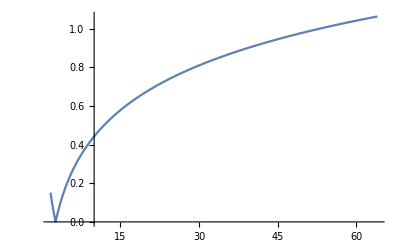

```mathematica
Plot[ratioCrossSection[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioCrossSection[(2mc)^2]
```

0.311671

```mathematica
CrossSectionRatio=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]]]/.{mmu-> m^2}
```

0.787739

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 m)^2}],10^(-9)]
```

4.794 z^3+3.83191 z^2

```mathematica
(* 
sqrt(s)=15.1047 GeV sigma(PV)=50.5894 fb+59.4964 fb
sqrt(s)=22.6047 GeV sigma(PV)=3.83191 fb+4.74396 fb
sqrt(s)=27.6047 GeV sigma(PV)=0.885096 fb+1.1434 fb
*)
```